Coherent Vision II

```mathematica
W=1;
kW=10^3;
MW=10^6;
J=1;
mJ=10^-3;
μJ=10^-6;
nJ=10^-9;
kJ=10^3;
mm=10^-3;
nm=10^-9;
cm=10^-2;
MHz=10^6;
fs=10^-15;
```

```mathematica
Pavg=3 W; (*average power*)
λ=800 nm;(*wavelength*)
r=0.6mm; (*radius*)
f=80 MHz; (*repetition rate*)
Δt=140 fs;(*pulse width*)
```

Average and peak values

```mathematica
EE=Pavg/f;(*average energy per cycle*)
nE=EE/(π r^2);(*average energy density*)
II=Pavg/(π r^2);(*average intensity*)
Ppeak=Pavg/(Δt f);(*peak power*)
Epeak=Ppeak/f;(*peak energy*)
nEpeak=Epeak/(π r^2);(*peak energy density*)
Ipeak=Ppeak/(π r^2);(*peak intensity*)
```

```mathematica
Grid[{{"","Average","","Peak",""},
{"Power P",Pavg,"W",1.Ppeak/kW,"kW"},
{"Intensity I",II/(W/cm^2),"W/cm^2", Ipeak/(MW/cm^2),"MW/cm^2" },
{"Energy E",1.EE/nJ,"nJ",1.Epeak/mJ ,"mJ"},
{"Energy density nE",1.nE/(μJ/cm^2),"μJ/cm^2", 1.nEpeak/(mJ/cm^2),"mJ/cm^2" }},Frame->All]
```

| Average |  | Peak | 
Power P | 3 | W | 267.857 | kW
Intensity I | 265.258 | W/cm^2 | 23.6838 | MW/cm^2
Energy E | 37.5 | nJ | 3.34821 | mJ
Energy density nE | 3.31573 | μJ/cm^2 | 296.047 | mJ/cm^2

Damage threshold (LDT)
Ref: http://www.semrock.com/laser-damage-threshold.aspx

```mathematica
(*LDT = 2J/cm^2;*)(*laser damage threshold*)
λspec=800nm;(*wavelength at which the LDT is specified*)

LDTcor[LDT_]=10000 W/J λ/λspec LDT;(*corrected LDT. For fs pulse at MHz repetition, the laser behaves as CW. However, this formula is only an estimation!! *)


LDTcor[2 J/cm^2]/(W/cm^2)
```

20000

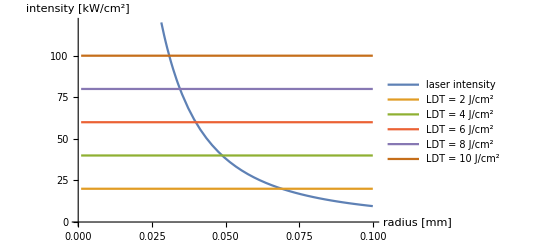

```mathematica
Intensity[r_]:=Pavg/(π r^2)(*gaussian beam peak intensity*)
Plot[{Intensity[r mm]/(kW/cm^2),Evaluate[Table[LDTcor[x J/cm^2]/(kW/cm^2),{x,2,10,2}]]},{r,0.001,0.1},AxesLabel->{"radius [mm]","intensity [kW/cm^2]"},PlotLegends->{"laser intensity","LDT = 2 J/cm^2","LDT = 4 J/cm^2","LDT = 6 J/cm^2","LDT = 8 J/cm^2","LDT = 10 J/cm^2"},PlotRange->{0,120}]
```

```mathematica
Intensity[0.04mm]/(W/cm^2)
```

59683.1